```mathematica
(* Parameters of the nanostructure *)
```

```mathematica
Subscript[h, lead]=150; Subscript[w, lead]=13; Subscript[l, lead]=500;(*nm*)
Subscript[h, cons]=35; Subscript[w, cons]=13; Subscript[l, cons]=400; (*nm*)
Subscript[l, cone]=50; (*nm*)
Subscript[l, 0]=Subscript[l, lead]; Subscript[l, 1]=Subscript[l, 0]+Subscript[l, cone]; Subscript[l, 2]=Subscript[l, 1]+Subscript[l, cons]; Subscript[l, 3]=Subscript[l, 2]+Subscript[l, cone]; Subscript[l, 4] =Subscript[l, 3]+Subscript[l, lead];
Subscript[R, 0]=(2*Subscript[h, lead] + 2*Subscript[w, lead])/ (2*Pi);Subscript[R, 1]=(2*Subscript[h, cons] + 2*Subscript[w, cons])/ (2*Pi);
vf=5*10^(5) (*m/s*); hbar = 1.05*10^(-34)(*Js*); eV=1.6*10^(-19)(*C*); nm=1*10^(-9); (*m*)
B=3.5(*T*); Subscript[ϕ, 0]=2*Pi*hbar/eV(*Tm.b2*); σ=10 * 10^(-3); (*nm⁻.b9*)
const = vf *hbar * 10^(3)/ eV; (*meV * m*)
(*Subscript[l, 0]=0; Subscript[l, 1]=594.7;Subscript[l, 4]=Subscript[l, 1]; Subscript[R, 0]=156.6; Subscript[R, 1]=Subscript[R, 0]/2;*)


(* Functions of R(x)*)
flux[r_]:=Pi*B*nm^2*r^2   (* Flux through the nanostructure Tm.b2*)

Θ[σ_, x1_, x2_]:= 0.5+ ArcTan[σ*(x1-x2)]/Pi (* Smoothing function for the step functions*)

Subscript[R, cone][x_, r0_, r1_, x0_, x1_, σ_]:=r0 + (r1-r0)*Θ[σ,x,x1]+(r1-r0)/(x1-x0)*(x-x0)*(Θ[σ,x,x0]-Θ[σ,x,x1]) (*Radius of a nanocone nm*)

Subscript[R, DB][x_, σ_]:=Subscript[R, cone][x,Subscript[R, 0],Subscript[R, 1],Subscript[l, 0],Subscript[l, 1],σ]+Subscript[R, cone][-x+Subscript[l, 1]+Subscript[l, 2],Subscript[R, 0],Subscript[R, 1],Subscript[l, 0],Subscript[l, 1],σ]-Subscript[R, 1] (*nm*)  (*Radius of the full nanostructure*)

Subscript[dR, DB][x_]:= D[Subscript[R, DB][y,σ], y]/.y->x

Subscript[d.b2R, DB][x_]:= D[Subscript[R, DB][y,σ], y,y]/.y->x   (* 1/nm *)

γ[x_]:=1/(√(1+Subscript[dR, DB][x]^2)) 

V[x_,l_]:=-(const/(nm*Subscript[R, DB][x,σ]))*(l+0.5- flux[Subscript[R, DB][x,σ]]/Subscript[ϕ, 0]) (*Centrifugal potential along the naostructure  meV*)

Subscript[V, g][x_,val_]:=val*(Θ[σ,x,Subscript[l, 1]]-Θ[σ,x,Subscript[l, 2]]) (*Gate potential  meV*)

kl[x_,l_]:=V[x,l]*nm/const  (*angular momentum*)

dkl[x_,l_]:=D[kl[y,l], y]/.y->x

Subscript[F, 1][x_]:=-Subscript[dR, DB][x]*((γ[x]^2)*Subscript[d.b2R, DB][x]-1/(Subscript[R, DB][x,σ])) 

Subscript[F, 0][x_,l_]:=(-kl[x,l]^2)/γ[x]^2+(1/(2 Subscript[R, DB][x,σ]))*(γ[x]^2*Subscript[d.b2R, DB][x]-(Subscript[dR, DB][x]^2)/(2 Subscript[R, DB][x,σ])) 

Subscript[F, pm][x_,l_]:=dkl[x,l]/γ[x]
```

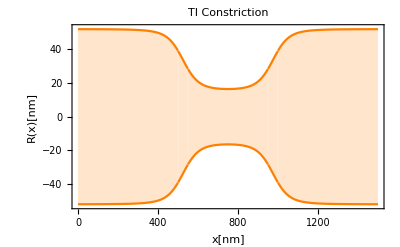

```mathematica
(* Nanostructure plot *)
Plot[{Subscript[R, DB][x,0.01],-Subscript[R, DB][x,0.01]},{x,0,Subscript[l, 4]},PlotRange->{{0,Subscript[l, 4]},{-Subscript[R, 0]-0.5,Subscript[R, 0]+0.5}}, FrameLabel->{"x[nm]","R(x)[nm]"},PlotStyle->Orange, Frame->True,  PlotLabel->Style["TI Constriction"], Filling->{1->{2}}]
```

```mathematica
(* Centrifugal potential along the nanostructure as a function of B and Subscript[V, g]*)
(*We define these two functions just to plot easily, to solve the diff equation use the previously defined*)
Subscript[V, plot][x_,l_,mag_]:=-(const/(nm*Subscript[R, DB][x,σ]))*(l+0.5- (Pi*mag*nm^2*Subscript[R, DB][x,σ]^2)/Subscript[ϕ, 0]) (*meV*)
Subscript[V, tot][x_, l_, gate_, field_]:=Abs[Subscript[V, plot][x,l,field]+Subscript[V, g][x,gate]]

Manipulate[Plot[Evaluate@Table[Subscript[V, tot][x,a,gate,field],{a,-10,10,1}],{x,0,Subscript[l, 4]},PlotRange->{{0,Subscript[l, 4]},{0, 50}}, FrameLabel->{"x[nm]","V_l(x)[meV]"}, Frame->True, GridLinesStyle->Directive[Black, Thick, Dashed], ImageSize->Medium, PlotLegends->LineLegend[Table[a,{a,-10,10,1}]]],{gate,-100, 100},{field,0, 5}]
```

```mathematica
(* Bound states and energy levels on the constriction*)
Subscript[𝒪, p1]=-(γ[x]^2)*(u''[x]+Subscript[F, 1][x]*u'[x]+(Subscript[F, 0][x,1]+Subscript[F, pm][x,1])*u[x]); (*Diff operator for +*)
Subscript[𝒪, m1]=-(γ[x]^2)*(u''[x]+Subscript[F, 1][x]*u'[x]+(Subscript[F, 0][x,1]-Subscript[F, pm][x,1])*u[x]); (* Diff operator for -*)
{SubPlus[vals],SubPlus[funs]}=NDEigensystem[{Subscript[𝒪, p1]},u[x],{x,0,Subscript[l, 4]},25]; (* Spectrum for +*)
{SubMinus[vals],SubMinus[funs]}=NDEigensystem[{Subscript[𝒪, m1]},u[x],{x,0,Subscript[l, 4]},25]; (*Spectrum for -*)
Subscript[χ, 1]=0.5*(SubPlus[funs]+SubMinus[funs]); Subscript[χ, 2]=0.5*(SubPlus[funs]-SubMinus[funs]); (* Spin up spin down components*)
Energy = Sqrt[(hbar*vf/nm)^2 *SubPlus[vals]]*10^3/eV; Subscript[ψ, 1] =3000*(Subscript[χ, 1]*Conjugate[Subscript[χ, 1]]);  Subscript[ψ, 2] =3000*(Subscript[χ, 2]*Conjugate[Subscript[χ, 2]]); (* Energy and probability densities*)

Show[Plot[Evaluate[ Subscript[ψ, 1]+Energy],{x,0,Subscript[l, 4]},FrameLabel->{"x[nm]","V_l(x)[meV], χ_+.b2[arb.]"}, PlotLegends->Automatic, Frame->True, PlotRange->{{0,Subscript[l, 4]},{-0.5, 50}}],
Plot[Evaluate[ Subscript[ψ, 2]+Energy],{x,0,Subscript[l, 4]},FrameLabel->{"x[nm]","V_l(x)[meV], χ_+.b2[arb.]"}, Frame->True, PlotStyle->Dashed,PlotRange->{{0,Subscript[l, 4]},{-0.5, 50}}],
Plot[Abs[V[x,1]],{x,0,Subscript[l, 4]},PlotStyle->Black],PlotLabel->Style[B "T"]]
Energy
```

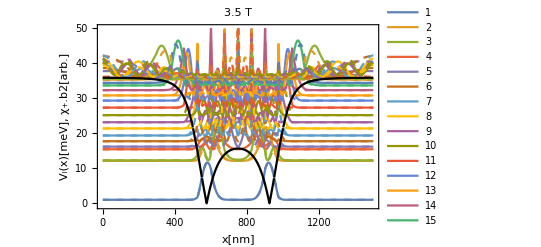

Table::itform: Argument {a,0,1,2,3,4,5} at position 2 does not have the correct form for an iterator.

General::stop: Further output of Table::itform will be suppressed during this calculation.